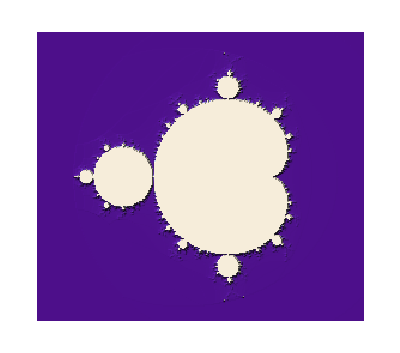

```mathematica
eTime[z0_,maxIter_Integer: 100]:=(Length@NestWhileList[(#+z0)^2&,0,(Abs@#≤2)&,1,maxIter])-1

DistributeDefinitions[eTime];
mesh=ParallelTable[eTime[(x+I*y),1000],{y,1.2,-1.2,-0.01},{x,-1.72,1,0.01}];
ReliefPlot[mesh,Frame->False]
```